```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using Quantis as a source of randomness.

Note: You should configure this backend with QuantisSetDevice function by providing information about the type and id of the used Quantis device.

Note: By default the package will use a USB Quantis device with id set to 0.

Quantis tests

```mathematica
QuantisSetDevice["USB",0]
```

Using Quantis device: type=USB, id=0

```mathematica
maxN=7;
quantisListTimings=Table[-1.0,{maxN}];
```

```mathematica
quantisListTimings=Table[{ii,AbsoluteTiming[TrueRandomReal[{0,1},10^ii]][[1]]},{ii,1,maxN}];
```

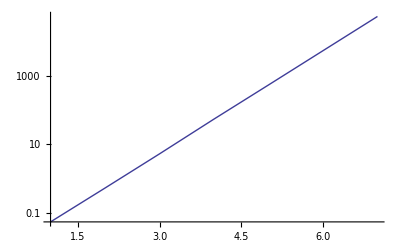

```mathematica
ListLogPlot[quantisListTimings,Joined->True]
```

```mathematica
Export["quantis_list_maxN=7.dat",quantisListTimings]
```

quantis_list_maxN=7.dat

```mathematica
quantisListTimings
```

{{1,0.055092},{2,0.534579},{3,5.296197},{4,54.692001},{5,539.089623},{6,5373.639893},{7,53501.220299}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS/timings/v_0.2.x